```mathematica
g3Data=Import["/Users/benxgh1996/Desktop/Rutherford/data.xlsx",{"Data",1,Range[2,19],{2}}]
```

{333.,265.,366.,585.,761.,1509.,745.,655.,464.,318.,201.,103.,145.,380.,90.,88.,100.,675.}

```mathematica
confiLower[number_,percent_]:=
Module[{k,α},
k=number;
α=1-percent;
1/2*Quantile[ChiSquareDistribution[2k],α/2]
]
```

```mathematica
confiUpper[number_,percent_]:=
Module[{k,α},
k=number;
α=1-percent;
1/2*Quantile[ChiSquareDistribution[2k+2],1-α/2]
]
```

```mathematica
g3dCopy=g3Data
```

{333.,265.,366.,585.,761.,1509.,745.,655.,464.,318.,201.,103.,145.,380.,90.,88.,100.,675.}

```mathematica
For[i=1,i≤Length[g3dCopy],i++,
g3dCopy[[i]]={g3dCopy[[i]],confiLower[g3dCopy[[i]],0.95],confiUpper[g3dCopy[[i]],0.95]}]
```

```mathematica
g3dCopy
```

{{333.,298.19,370.757},{265.,234.052,298.902},{366.,329.46,405.486},{585.,538.549,634.386},{761.,707.885,817.044},{1509.,1433.82,1587.1},{745.,692.457,800.473},{655.,605.792,707.14},{464.,422.736,508.203},{318.,284.005,354.943},{201.,174.172,230.791},{103.,84.0719,124.917},{145.,122.36,170.615},{380.,342.749,420.195},{90.,72.3706,110.625},{88.,70.5786,108.418},{100.,81.364,121.627},{675.,625.032,727.9}}

```mathematica
{confiLower[380,0.95],confiUpper[380,0.95]}
```

{342.749,420.195}

```mathematica
g3dCopy//TableForm
```

333. | 298.19 | 370.757
265. | 234.052 | 298.902
366. | 329.46 | 405.486
585. | 538.549 | 634.386
761. | 707.885 | 817.044
1509. | 1433.82 | 1587.1
745. | 692.457 | 800.473
655. | 605.792 | 707.14
464. | 422.736 | 508.203
318. | 284.005 | 354.943
201. | 174.172 | 230.791
103. | 84.0719 | 124.917
145. | 122.36 | 170.615
380. | 342.749 | 420.195
90. | 72.3706 | 110.625
88. | 70.5786 | 108.418
100. | 81.364 | 121.627
675. | 625.032 | 727.9

```mathematica
Export["confi.xlsx",g3dCopy]
```

confi.xlsx

```mathematica
a2Data=Import["/Users/benxgh1996/Desktop/Rutherford/data.xlsx",{"Data",2,Range[2,6],{2}}]
```

{1060.,2912.,2709.,1018.,48.}

```mathematica
a2dCopy=a2Data
```

{1060.,2912.,2709.,1018.,48.}

```mathematica
For[i=1,i≤Length[a2dCopy],i++,
a2dCopy[[i]]={a2dCopy[[i]],confiLower[a2dCopy[[i]],0.95],confiUpper[a2dCopy[[i]],0.95]}]
```

```mathematica
a2dCopy//TableForm
```

1060. | 997.141 | 1125.78
2912. | 2807.18 | 3019.73
2709. | 2607.94 | 2812.97
1018. | 956.418 | 1082.51
48. | 35.3914 | 63.641

```mathematica
{confiLower[1018,0.95],confiUpper[1018,0.95]}
```

{956.418,1082.51}

```mathematica
Export["confi.xlsx",a2dCopy]
```

confi.xlsx

```mathematica
g3cr=Import["/Users/benxgh1996/Desktop/Rutherford/data.xlsx",{"Data",1,Range[2,19],{1,6,7,8}}]
```

{{-15.,166.5,149.095,185.379},{-12.5,265.,234.052,298.902},{-10.,366.,329.46,405.486},{-7.5,585.,538.549,634.386},{-5.,761.,707.885,817.044},{-2.5,754.5,716.908,793.552},{0.,745.,692.457,800.473},{2.5,655.,605.793,707.14},{5.,464.,422.736,508.203},{7.5,318.,284.005,354.943},{10.,201.,174.172,230.791},{12.5,103.,84.0719,124.918},{15.,72.5,61.18,85.3074},{20.,25.3333,22.8499,28.013},{30.,4.5,3.61853,5.53126},{40.,1.46667,1.17631,1.80698},{50.,0.769231,0.625877,0.935591},{60.,0.24871,0.230299,0.268202}}

```mathematica
g3eList=g3cr
```

{{-15.,166.5,149.095,185.379},{-12.5,265.,234.052,298.902},{-10.,366.,329.46,405.486},{-7.5,585.,538.549,634.386},{-5.,761.,707.885,817.044},{-2.5,754.5,716.908,793.552},{0.,745.,692.457,800.473},{2.5,655.,605.793,707.14},{5.,464.,422.736,508.203},{7.5,318.,284.005,354.943},{10.,201.,174.172,230.791},{12.5,103.,84.0719,124.918},{15.,72.5,61.18,85.3074},{20.,25.3333,22.8499,28.013},{30.,4.5,3.61853,5.53126},{40.,1.46667,1.17631,1.80698},{50.,0.769231,0.625877,0.935591},{60.,0.24871,0.230299,0.268202}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
For[i=1,i≤Length[g3eList],i++,
negErr= g3eList[[i]][[3]]-g3eList[[i]][[2]];
posErr=g3eList[[i]][[4]]-g3eList[[i]][[2]];
g3eList[[i]]={{g3eList[[i]][[1]],g3eList[[i]][[2]]},ErrorBar[{negErr,posErr}]}
]
```

```mathematica
g3eList
```

{{{-15.,166.5},ErrorBar[{-17.4048,18.8786}]},{{-12.5,265.},ErrorBar[{-30.9485,33.9024}]},{{-10.,366.},ErrorBar[{-36.5404,39.4855}]},{{-7.5,585.},ErrorBar[{-46.4511,49.3856}]},{{-5.,761.},ErrorBar[{-53.1147,56.0444}]},{{-2.5,754.5},ErrorBar[{-37.5925,39.052}]},{{0.,745.},ErrorBar[{-52.5432,55.4733}]},{{2.5,655.},ErrorBar[{-49.2075,52.1399}]},{{5.,464.},ErrorBar[{-41.2639,44.2034}]},{{7.5,318.},ErrorBar[{-33.9946,36.9434}]},{{10.,201.},ErrorBar[{-26.8284,29.7911}]},{{12.5,103.},ErrorBar[{-18.9281,21.9175}]},{{15.,72.5},ErrorBar[{-11.3201,12.8074}]},{{20.,25.3333},ErrorBar[{-2.48339,2.67967}]},{{30.,4.5},ErrorBar[{-0.881468,1.03126}]},{{40.,1.46667},ErrorBar[{-0.290357,0.340308}]},{{50.,0.769231},ErrorBar[{-0.143354,0.16636}]},{{60.,0.24871},ErrorBar[{-0.0184111,0.0194913}]}}

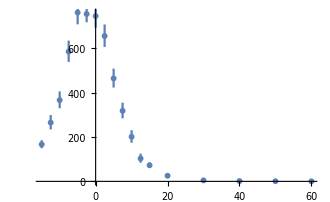

```mathematica
ErrorListPlot[g3eList]
```

```mathematica
g3elCopy=g3eList
```

{{{-15.,166.5},ErrorBar[{-17.4048,18.8786}]},{{-12.5,265.},ErrorBar[{-30.9485,33.9024}]},{{-10.,366.},ErrorBar[{-36.5404,39.4855}]},{{-7.5,585.},ErrorBar[{-46.4511,49.3856}]},{{-5.,761.},ErrorBar[{-53.1147,56.0444}]},{{-2.5,754.5},ErrorBar[{-37.5925,39.052}]},{{0.,745.},ErrorBar[{-52.5432,55.4733}]},{{2.5,655.},ErrorBar[{-49.2075,52.1399}]},{{5.,464.},ErrorBar[{-41.2639,44.2034}]},{{7.5,318.},ErrorBar[{-33.9946,36.9434}]},{{10.,201.},ErrorBar[{-26.8284,29.7911}]},{{12.5,103.},ErrorBar[{-18.9281,21.9175}]},{{15.,72.5},ErrorBar[{-11.3201,12.8074}]},{{20.,25.3333},ErrorBar[{-2.48339,2.67967}]},{{30.,4.5},ErrorBar[{-0.881468,1.03126}]},{{40.,1.46667},ErrorBar[{-0.290357,0.340308}]},{{50.,0.769231},ErrorBar[{-0.143354,0.16636}]},{{60.,0.24871},ErrorBar[{-0.0184111,0.0194913}]}}

```mathematica
g3crList=#[[1]]&/@g3elCopy
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{-7.5,585.},{-5.,761.},{-2.5,754.5},{0.,745.},{2.5,655.},{5.,464.},{7.5,318.},{10.,201.},{12.5,103.},{15.,72.5},{20.,25.3333},{30.,4.5},{40.,1.46667},{50.,0.769231},{60.,0.24871}}

```mathematica
g3clCopy=g3crList
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{-7.5,585.},{-5.,761.},{-2.5,754.5},{0.,745.},{2.5,655.},{5.,464.},{7.5,318.},{10.,201.},{12.5,103.},{15.,72.5},{20.,25.3333},{30.,4.5},{40.,1.46667},{50.,0.769231},{60.,0.24871}}

```mathematica
{First@#,Log@Last@#}&/@g3elCopy
```

{{{-15.,166.5},Log[ErrorBar[{-17.4048,18.8786}]]},{{-12.5,265.},Log[ErrorBar[{-30.9485,33.9024}]]},{{-10.,366.},Log[ErrorBar[{-36.5404,39.4855}]]},{{-7.5,585.},Log[ErrorBar[{-46.4511,49.3856}]]},{{-5.,761.},Log[ErrorBar[{-53.1147,56.0444}]]},{{-2.5,754.5},Log[ErrorBar[{-37.5925,39.052}]]},{{0.,745.},Log[ErrorBar[{-52.5432,55.4733}]]},{{2.5,655.},Log[ErrorBar[{-49.2075,52.1399}]]},{{5.,464.},Log[ErrorBar[{-41.2639,44.2034}]]},{{7.5,318.},Log[ErrorBar[{-33.9946,36.9434}]]},{{10.,201.},Log[ErrorBar[{-26.8284,29.7911}]]},{{12.5,103.},Log[ErrorBar[{-18.9281,21.9175}]]},{{15.,72.5},Log[ErrorBar[{-11.3201,12.8074}]]},{{20.,25.3333},Log[ErrorBar[{-2.48339,2.67967}]]},{{30.,4.5},Log[ErrorBar[{-0.881468,1.03126}]]},{{40.,1.46667},Log[ErrorBar[{-0.290357,0.340308}]]},{{50.,0.769231},Log[ErrorBar[{-0.143354,0.16636}]]},{{60.,0.24871},Log[ErrorBar[{-0.0184111,0.0194913}]]}}

```mathematica
{#[[1]],Log@#[[2]]}&/@g3crList
```

{{-15.,5.115},{-12.5,5.57973},{-10.,5.90263},{-7.5,6.37161},{-5.,6.63463},{-2.5,6.62606},{0.,6.61338},{2.5,6.48464},{5.,6.13988},{7.5,5.76205},{10.,5.3033},{12.5,4.63473},{15.,4.28359},{20.,3.23212},{30.,1.50408},{40.,0.382992},{50.,-0.262364},{60.,-1.39147}}

```mathematica
NonlinearModelFit[{#[[1]],Log@#[[2]]}&/@g3crList,{Log[k/Sin[(θ-θ0)/2*π/180]^4],{k>0,θ0>-2.5,θ0<0}},{k,θ0},θ]
```

FittedModel[Log[0.00537122 Csc[1/360 π (1.23986+θ)]^4]]

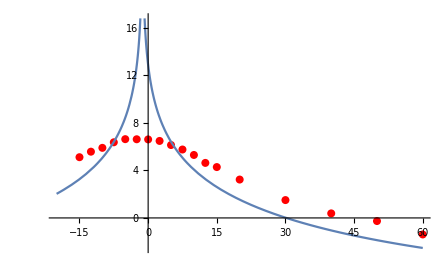

```mathematica
Show[ListPlot[{#[[1]],Log@#[[2]]}&/@g3crList,PlotStyle->Red],Plot[Log[0.005371215397349859 Csc[1/360 π (1.2398646831648719+θ)]^4],{θ,-20,60}],PlotRange->All]
```

```mathematica
{1/Sin[1/2(First@#+3.6918377219920986)*π/180]^4,Last@#}&/@g3crList
```

{{10613.6,166.5},{28759.4,265.},{109113.,366.},{820481.,585.},{5.88846×10^7,761.},{8.54621×10^7,754.5},{928839.,745.},{117538.,655.},{30327.,464.},{11060.3,318.},{4953.35,201.},{2542.2,103.},{1437.85,72.5},{563.131,25.3333},{141.779,4.5},{52.1562,1.46667},{24.0443,0.769231},{12.9021,0.24871}}

```mathematica
g3crList
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{-7.5,585.},{-5.,761.},{-2.5,754.5},{0.,745.},{2.5,655.},{5.,464.},{7.5,318.},{10.,201.},{12.5,103.},{15.,72.5},{20.,25.3333},{30.,4.5},{40.,1.46667},{50.,0.769231},{60.,0.24871}}

```mathematica
Manipulate[ListPlot[{Log[1/Sin[1/2(First@#-θ0)*π/180]^4],Log[Last@#]}&/@g3crList],{θ0,-1.875,0,Appearance-> "Labeled"}]
```

ListPlot::lpn: g3crList is not a list of numbers or pairs of numbers.

Power::infy: Infinite expression 1/0. encountered.

ListPlot::lpn: g3crList is not a list of numbers or pairs of numbers.

Power::infy: Infinite expression 1/0. encountered.

ListPlot::lpn: g3crList is not a list of numbers or pairs of numbers.

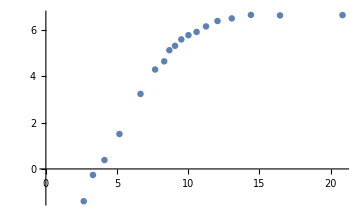

```mathematica
ListPlot@@({{Log[1/Sin[1/2(First@#-θ0)*π/180]^4],Log[Last@#]}&/@g3crList}/.{θ0-> -1.875})
```

```mathematica
g3crList
```

g3crList

```mathematica
llList={Log[1/Sin[1/2(First@#-θ0)*π/180]^4],Log[Last@#]}&/@g3crList/.{θ0-> -1.875}
```

{{8.67617,5.115},{9.51839,5.57973},{10.5891,5.90263},{12.0582,6.37161},{14.4083,6.63463},{20.8455,6.62606},{16.4512,6.61338},{13.0628,6.48464},{11.2563,6.13988},{10.0178,5.76205},{9.07492,5.3033},{8.31403,4.63473},{7.67663,4.28359},{6.64844,3.23212},{5.16992,1.50408},{4.11617,0.382992},{3.30772,-0.262364},{2.66133,-1.39147}}

```mathematica
FindFit[llList,x+a,{a},x]
```

{a→-5.27424}

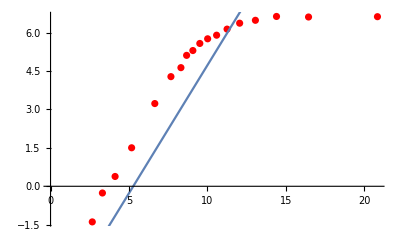

```mathematica
Show[ListPlot[llList,PlotStyle->Red],Plot[x+a/.{a->-5.274243391022774},{x,2.6613285683043997,20.845530931268897}]]
```

```mathematica
g3crList
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{-7.5,585.},{-5.,761.},{-2.5,754.5},{0.,745.},{2.5,655.},{5.,464.},{7.5,318.},{10.,201.},{12.5,103.},{15.,72.5},{20.,25.3333},{30.,4.5},{40.,1.46667},{50.,0.769231},{60.,0.24871}}

```mathematica
getLL[θ0_,diff_]:={Log[1/Sin[1/2(First@#-θ0)*π/180]^4],Log[Last@#]}&/@Select[g3crList,Abs[First@#-θ0]≥diff&]
```

```mathematica
llList=getLL[-1.875,10]
```

{{8.67617,5.115},{9.51839,5.57973},{9.07492,5.3033},{8.31403,4.63473},{7.67663,4.28359},{6.64844,3.23212},{5.16992,1.50408},{4.11617,0.382992},{3.30772,-0.262364},{2.66133,-1.39147}}

```mathematica
FindFit[llList,x+a,{a},x]
```

{a→-3.6782}

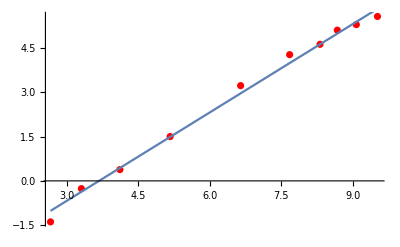

```mathematica
Show[ListPlot[llList,PlotStyle->Red],Plot[x+a/.{a->-3.678201278149144},{x,2.6613285683043997,9.518390774994637}]]
```

```mathematica
Select[g3crList,Abs[#[[1]]-θ0]≥15&/.{θ0-> -1.875}]
```

{{15.,72.5},{20.,25.3333},{30.,4.5},{40.,1.46667},{50.,0.769231},{60.,0.24871}}

```mathematica
x+a/.{x-> Log[1/Sin[1/2(23.75)*π/180]^4],a->-3.678201278149144}
```

2.64564

```mathematica
ⅇ^2.6456435095760646
```

14.0925

```mathematica
g3cr
```

{{-15.,166.5,149.095,185.379},{-12.5,265.,234.052,298.902},{-10.,366.,329.46,405.486},{-7.5,585.,538.549,634.386},{-5.,761.,707.885,817.044},{-2.5,754.5,716.908,793.552},{0.,745.,692.457,800.473},{2.5,655.,605.793,707.14},{5.,464.,422.736,508.203},{7.5,318.,284.005,354.943},{10.,201.,174.172,230.791},{12.5,103.,84.0719,124.918},{15.,72.5,61.18,85.3074},{20.,25.3333,22.8499,28.013},{30.,4.5,3.61853,5.53126},{40.,1.46667,1.17631,1.80698},{50.,0.769231,0.625877,0.935591},{60.,0.24871,0.230299,0.268202}}

```mathematica
g3crs=Select[g3cr,Abs[#[[1]]+1.875]≥10&]
```

{{-15.,166.5,149.095,185.379},{-12.5,265.,234.052,298.902},{10.,201.,174.172,230.791},{12.5,103.,84.0719,124.918},{15.,72.5,61.18,85.3074},{20.,25.3333,22.8499,28.013},{30.,4.5,3.61853,5.53126},{40.,1.46667,1.17631,1.80698},{50.,0.769231,0.625877,0.935591},{60.,0.24871,0.230299,0.268202}}

```mathematica
g3crs
```

{{-15.,166.5,149.095,185.379},{-12.5,265.,234.052,298.902},{10.,201.,174.172,230.791},{12.5,103.,84.0719,124.918},{15.,72.5,61.18,85.3074},{20.,25.3333,22.8499,28.013},{30.,4.5,3.61853,5.53126},{40.,1.46667,1.17631,1.80698},{50.,0.769231,0.625877,0.935591},{60.,0.24871,0.230299,0.268202}}

```mathematica
g3lls={Log[1/Sin[1/2(#[[1]]-θ0)*π/180]^4],Log[#[[2]]],Log[#[[3]]],Log[#[[4]]]}/.{θ0-> -1.875}&/@g3crs
```

{{8.67617,5.115,5.00459,5.2224},{9.51839,5.57973,5.45554,5.70012},{9.07492,5.3033,5.16004,5.44151},{8.31403,4.63473,4.43167,4.82765},{7.67663,4.28359,4.11382,4.44626},{6.64844,3.23212,3.12895,3.33267},{5.16992,1.50408,1.28607,1.71042},{4.11617,0.382992,0.162382,0.591654},{3.30772,-0.262364,-0.468602,-0.0665771},{2.66133,-1.39147,-1.46838,-1.31602}}

```mathematica
g3llb={Log[1/Sin[1/2(#[[1]]-θ0)*π/180]^4],Log[#[[2]]],Log[#[[3]]],Log[#[[4]]]}/.{θ0-> -1.875}&/@g3cr
```

{{8.67617,5.115,5.00459,5.2224},{9.51839,5.57973,5.45554,5.70012},{10.5891,5.90263,5.79745,6.00509},{12.0582,6.37161,6.28888,6.45266},{14.4083,6.63463,6.56228,6.70569},{20.8455,6.62606,6.57495,6.67652},{16.4512,6.61338,6.54025,6.6852},{13.0628,6.48464,6.40654,6.56123},{11.2563,6.13988,6.04675,6.23088},{10.0178,5.76205,5.64899,5.87196},{9.07492,5.3033,5.16004,5.44151},{8.31403,4.63473,4.43167,4.82765},{7.67663,4.28359,4.11382,4.44626},{6.64844,3.23212,3.12895,3.33267},{5.16992,1.50408,1.28607,1.71042},{4.11617,0.382992,0.162382,0.591654},{3.30772,-0.262364,-0.468602,-0.0665771},{2.66133,-1.39147,-1.46838,-1.31602}}

```mathematica
getLL[-1.875,0]
```

{{8.67617,5.115},{9.51839,5.57973},{10.5891,5.90263},{12.0582,6.37161},{14.4083,6.63463},{20.8455,6.62606},{16.4512,6.61338},{13.0628,6.48464},{11.2563,6.13988},{10.0178,5.76205},{9.07492,5.3033},{8.31403,4.63473},{7.67663,4.28359},{6.64844,3.23212},{5.16992,1.50408},{4.11617,0.382992},{3.30772,-0.262364},{2.66133,-1.39147}}

```mathematica
g3lle={{#[[1]],#[[2]]},ErrorBar[{#[[3]]-#[[2]],#[[4]]-#[[2]]}]}&/@g3llb
```

{{{8.67617,5.115},ErrorBar[{-0.11041,0.107405}]},{{9.51839,5.57973},ErrorBar[{-0.124189,0.120387}]},{{10.5891,5.90263},ErrorBar[{-0.10518,0.102452}]},{{12.0582,6.37161},ErrorBar[{-0.0827335,0.0810451}]},{{14.4083,6.63463},ErrorBar[{-0.0723513,0.0710601}]},{{20.8455,6.62606},ErrorBar[{-0.0511085,0.0504638}]},{{16.4512,6.61338},ErrorBar[{-0.0731384,0.071819}]},{{13.0628,6.48464},ErrorBar[{-0.0780977,0.0765933}]},{{11.2563,6.13988},ErrorBar[{-0.0931364,0.0909972}]},{{10.0178,5.76205},ErrorBar[{-0.113058,0.109907}]},{{9.07492,5.3033},ErrorBar[{-0.143264,0.138208}]},{{8.31403,4.63473},ErrorBar[{-0.203056,0.192925}]},{{7.67663,4.28359},ErrorBar[{-0.169767,0.162675}]},{{6.64844,3.23212},ErrorBar[{-0.103173,0.100548}]},{{5.16992,1.50408},ErrorBar[{-0.218009,0.206339}]},{{4.11617,0.382992},ErrorBar[{-0.22061,0.208662}]},{{3.30772,-0.262364},ErrorBar[{-0.206237,0.195787}]},{{2.66133,-1.39147},ErrorBar[{-0.0769094,0.0754503}]}}

```mathematica
g3se={{#[[1]],#[[2]]},ErrorBar[{#[[3]]-#[[2]],#[[4]]-#[[2]]}]}&/@g3lls
```

{{{8.67617,5.115},ErrorBar[{-0.11041,0.107405}]},{{9.51839,5.57973},ErrorBar[{-0.124189,0.120387}]},{{9.07492,5.3033},ErrorBar[{-0.143264,0.138208}]},{{8.31403,4.63473},ErrorBar[{-0.203056,0.192925}]},{{7.67663,4.28359},ErrorBar[{-0.169767,0.162675}]},{{6.64844,3.23212},ErrorBar[{-0.103173,0.100548}]},{{5.16992,1.50408},ErrorBar[{-0.218009,0.206339}]},{{4.11617,0.382992},ErrorBar[{-0.22061,0.208662}]},{{3.30772,-0.262364},ErrorBar[{-0.206237,0.195787}]},{{2.66133,-1.39147},ErrorBar[{-0.0769094,0.0754503}]}}

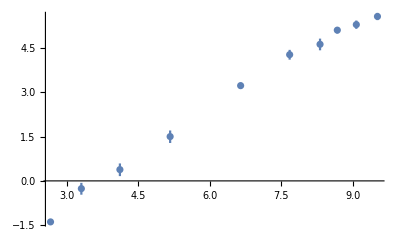

```mathematica
ErrorListPlot[g3se]
```

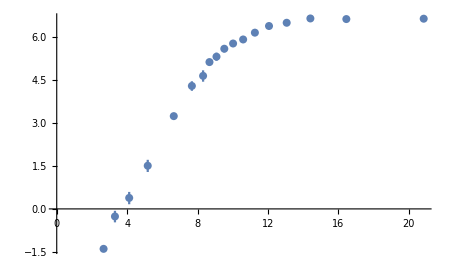

```mathematica
ErrorListPlot[g3lle]
```

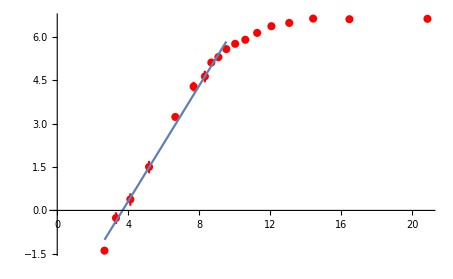

```mathematica
Show[ErrorListPlot[g3lle,PlotStyle->Red],Plot[x+a/.{a->-3.678201278149144},{x,2.6613285683043997,9.518390774994637}]]
```

```mathematica
a->-5.274243391022774
```

a→-5.27424

```mathematica
getlle[θ0_,diff_]:=Select[g3lle,Abs[#-θ0]≥diff&]
```

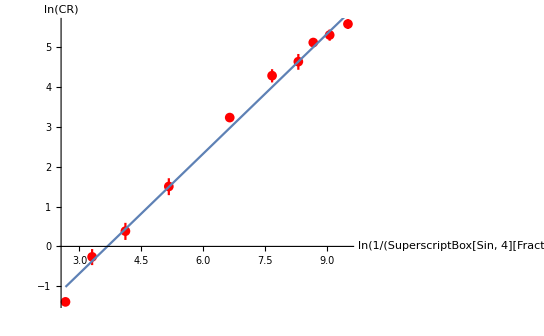

```mathematica
Show[ErrorListPlot[g3se,PlotStyle->Red],Plot[x+a/.{a->-3.678201278149144},{x,2.6613285683043997,9.518390774994637}],AxesLabel-> {"ln(1/(SuperscriptBox[Sin, 4][FractionBox[1, 2] (SubscriptBox[θ, c] - SubscriptBox[θ, 0])]))","ln(CR)"},BaseStyle->{FontSize->12}]
```

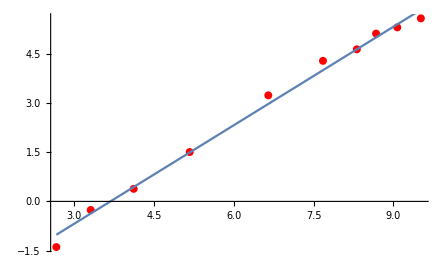

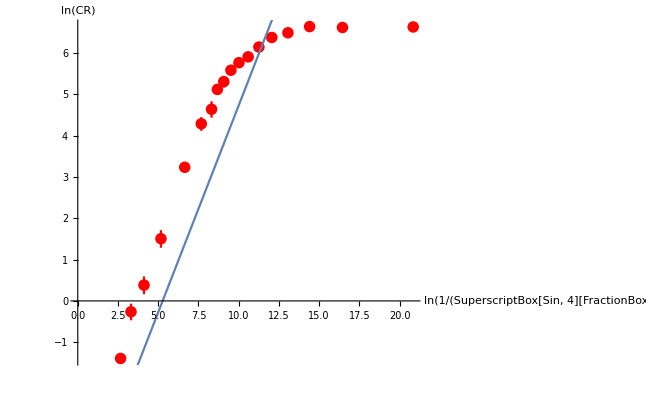

```mathematica
Show[ErrorListPlot[g3lle,PlotStyle->Red],Plot[x+a/.{a->-5.274243391022774},{x,2.6613285683043997,20.845530931268897}],AxesLabel-> {"ln(1/(SuperscriptBox[Sin, 4][FractionBox[1, 2] (SubscriptBox[θ, c] - SubscriptBox[θ, 0])]))","ln(CR)"},BaseStyle->{FontSize->12}]
```

```mathematica
g4=Import["/Users/benxgh1996/Desktop/Rutherford/data.xlsx",{"Data",3,Range[1,50],1}]
```

{140.,128.,130.,113.,113.,127.,123.,130.,117.,131.,105.,141.,137.,115.,127.,117.,132.,123.,136.,106.,139.,103.,120.,133.,111.,136.,140.,126.,130.,136.,134.,105.,127.,111.,119.,128.,113.,119.,130.,116.,120.,143.,117.,113.,123.,113.,103.,126.,126.,128.}

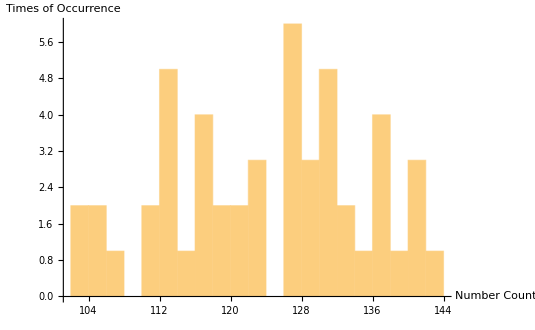

```mathematica
Histogram[g4,20,AxesLabel-> {"Number Count","Times of Occurrence"},BaseStyle->{FontSize->16}]
```

```mathematica
Mean[g4]
```

123.58

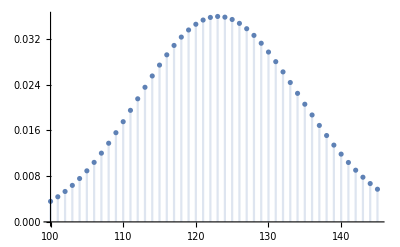

```mathematica
DiscretePlot[PDF[PoissonDistribution[Mean[g4]],x],{x,100,145}]
```

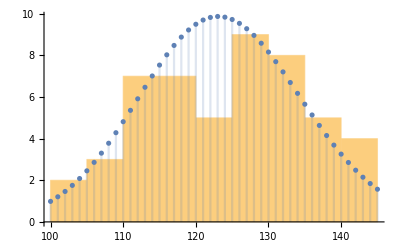

```mathematica
Show[Histogram[g4,10],DiscretePlot[275*PDF[PoissonDistribution[Mean[g4]],x],{x,100,145}]]
```